```mathematica
δ = E^(-3);
```

```mathematica
chainDist[r_,n_]:= If[r!=1,ProbabilityDistribution[(1-r)/(1-r^n)*r^(n-x),{x,1,n,1}], 
ProbabilityDistribution[1/n,{x,1, n, 1}]];
```

```mathematica
PDF[chainDist[2/3,10],10]
```

19683/58025

```mathematica
ResourceFunction["KullbackLeiblerDivergence"][chainDist[1,10], chainDist[2/3,10]]
```

Log[11605/(2592 √6)]

```mathematica
N[Out[27]]
```

%27

```mathematica
ResourceFunction["KullbackLeiblerDivergence"][chainDist[3/2,10], chainDist[2/3,10]]
```

1/58025(-19171 Log[58025/19683]-12354 Log[58025/13122]-7596 Log[58025/8748]-4104 Log[58025/5832]-1296 Log[58025/3888]+1296 Log[58025/2592]+4104 Log[58025/1728]+7596 Log[58025/1152]+12354 Log[58025/768]+19171 Log[58025/512])

```mathematica
N[Out[32]]
```

%32

```mathematica
ResourceFunction["KullbackLeiblerDivergence"][chainDist[3/2,10], chainDist[1,10]]+ ResourceFunction["KullbackLeiblerDivergence"][chainDist[1,10], chainDist[2/3,10]]
```

1/58025(-19683 Log[58025/19683]-13122 Log[58025/13122]-8748 Log[58025/8748]-5832 Log[58025/5832]+58025 Log[10]-3888 Log[58025/3888]-2592 Log[58025/2592]-1728 Log[58025/1728]-1152 Log[58025/1152]-768 Log[58025/768]-512 Log[58025/512])+Log[11605/(2592 √6)]

```mathematica
ϕ[n_,x_]:= If[x!=1,(x-n*x^n+(n-1)x^(n+1))/((1-x)(1-x^n)), (n-1)/2];
```

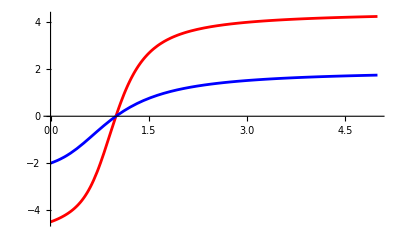

```mathematica
Plot[{ϕ[10,x]-9/2,ϕ[5,x]-4/2},{x,0,5}, PlotStyle->{Red, Blue}]
```

```mathematica
Limit[ϕ[10,x],x->0]
```

0

```mathematica
RecurrenceTable[{a[m+1]==a[m]*Exp[1/N[ϕ[10,a[m]]]], a[1]==1/δ}, a,{m,1,10}]
```

{ⅇ^3,22.4606,25.1146,28.0805,31.3949,35.0987,39.2377,43.8631,49.032,54.8083}

```mathematica
N[Exp[1/ϕ[10,1/δ]]]
```

1.11825

```mathematica
Series[ϕ[10,x]^(-1), x->0]
```

Piecewise[{{ComplexInfinity, x==0}, {1/x+O[x]^0, True}}]

```mathematica
ϕ[n_,x_]:= (x-n*x^n+(n-1)x^(n+1))/((1-x)(1-x^n))
```

```mathematica
N[ϕ[10, 3]]
```

8.50017

```mathematica
Series[ϕ[n,x], {x,0,2}]
```

(x+x^2+O[x]^3)/(1-x^n)+(x^n (-n-x-x^2+O[x]^3))/(1-x^n)

```mathematica
f[c_, n_, x_]:= ϕ[n, Exp[-c*x]];
```

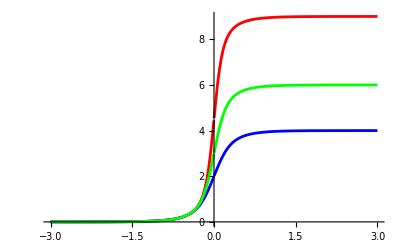

```mathematica
Plot[{f[-3,10,x],f[-3,5,x],f[-3,7,x] },{x,-3,3}, PlotStyle->{Red, Blue, Green}]
```

```mathematica
upperBarriers = ParallelTable[{n,NSolve[ϕ[n,x]==3/4*(n-1)&&x>0, x, Reals, WorkingPrecision->100]}, {n,5,80}];
```

```mathematica
upperBarriers[[All,2]] = Flatten[x /. upperBarriers[[All,2]] ];
```

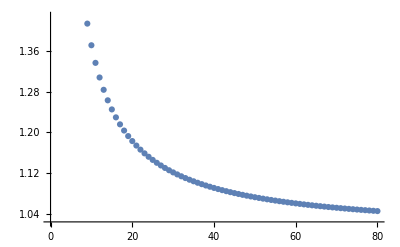

```mathematica
ListPlot[upperBarriers]
```

```mathematica
lowerBarriers = ParallelTable[{n,NSolve[ϕ[n,x]==1/4*(n-1)&&x>0, x, Reals, WorkingPrecision->100]}, {n,5,80}];
```

```mathematica
lowerBarriers[[All, 2]] = Flatten[x /. lowerBarriers[[All,2]]];
```

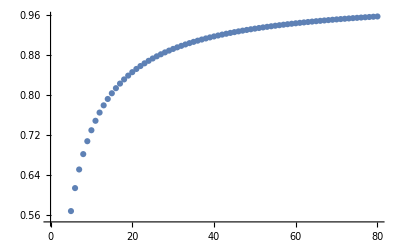

```mathematica
ListPlot[lowerBarriers]
```

```mathematica
barrierWidth = upperBarriers;
```

```mathematica
barrierWidth[[All, 2]] = barrierWidth[[All,2]] - lowerBarriers[[All,2]];
```

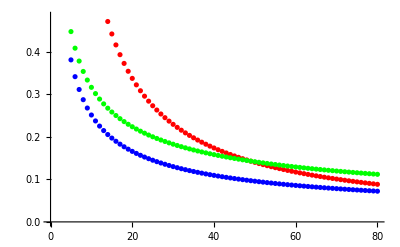

```mathematica
ListPlot[{barrierWidth, Table[{n,1/n^(3/5)}, {n,5,80}],Table[{n,1/n^(1/2)}, {n,5,80}]},PlotStyle->{Red, Blue, Green}]
```

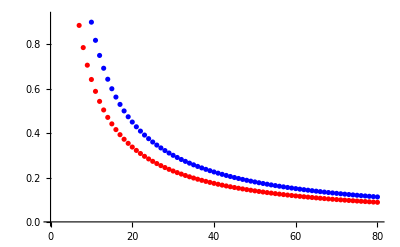

```mathematica
ListPlot[{barrierWidth, Table[{n,9/n}, {n,5,80}]},PlotStyle->{Red, Blue}]
```

```mathematica
logBarrierWidth = barrierWidth;
```

```mathematica
logBarrierWidth[[All,2]] = (Log[upperBarriers[[All,2]]/lowerBarriers[[All,2]]]);
```

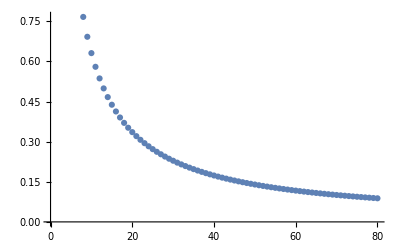

```mathematica
ListPlot[logBarrierWidth]
```

```mathematica
sqrtIntervalVariation = Table[{n,f[Exp[-3], n, 1-1/Sqrt[n]]-f[Exp[-3], n, 1+1/Sqrt[n]]}, {n,5,50}];
```

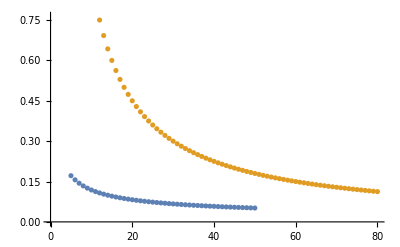

```mathematica
ListPlot[{sqrtIntervalVariation,  Table[{n,9/n}, {n,5,80}]}]
```

```mathematica
phiPrime[n_,x_] =If[x!=1,Derivative[0,1][ϕ][n,x],1/12(n^2-1)];
```

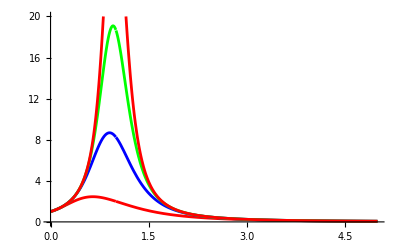

```mathematica
Plot[{phiPrime[5,x],phiPrime[10,x],phiPrime[15,x],phiPrime[20,x]},{x,0,5},PlotStyle->{Red,Blue,Green},PlotRange->{Automatic, {0,20}}]
```

```mathematica
phiPrime[n,x]
```

If[x≠1,ϕ^(0,1)[n,x],1/12 (n^2-1)]

```mathematica
peakGradientWidth = ParallelTable[{n,NSolve[phiPrime[n,x]== 1/24*(n^2-1)&&x>0,x]}, {n,5,80}];
```

```mathematica
peakGradientWidth = peakGradientWidth[[2;;]]
```

{{6,{{x→0.173525},{x→1.50431}}},{7,{{x→0.299006},{x→1.45358}}},{8,{{x→0.393506},{x→1.41141}}},{9,{{x→0.466695},{x→1.37601}}},{10,{{x→0.524764},{x→1.34596}}},{11,{{x→0.571808},{x→1.3202}}},{12,{{x→0.610612},{x→1.2979}}},{13,{{x→0.643119},{x→1.27843}}},{14,{{x→0.670717},{x→1.26129}}},{15,{{x→0.694423},{x→1.24611}}},{16,{{x→0.714993},{x→1.23257}}},{17,{{x→0.733004},{x→1.22042}}},{18,{{x→0.7489},{x→1.20946}}},{19,{{x→0.763028},{x→1.19952}}},{20,{{x→0.775667},{x→1.19048}}},{21,{{x→0.787036},{x→1.18221}}},{22,{{x→0.797318},{x→1.17463}}},{23,{{x→0.80666},{x→1.16764}}},{24,{{x→0.815184},{x→1.16119}}},{25,{{x→0.822992},{x→1.15522}}},{26,{{x→0.830172},{x→1.14967}}},{27,{{x→0.836794},{x→1.1445}}},{28,{{x→0.842922},{x→1.13967}}},{29,{{x→0.848608},{x→1.13516}}},{30,{{x→0.853899},{x→1.13092}}},{31,{{x→0.858834},{x→1.12695}}},{32,{{x→0.863448},{x→1.1232}}},{33,{{x→0.867771},{x→1.11967}}},{34,{{x→0.871829},{x→1.11634}}},{35,{{x→0.875647},{x→1.11318}}},{36,{{x→0.879244},{x→1.1102}}},{37,{{x→0.882639},{x→1.10736}}},{38,{{x→0.88585},{x→1.10467}}},{39,{{x→0.88889},{x→1.10211}}},{40,{{x→0.891772},{x→1.09967}}},{41,{{x→0.894509},{x→1.09734}}},{42,{{x→0.897111},{x→1.09512}}},{43,{{x→0.899589},{x→1.093}}},{44,{{x→0.90195},{x→1.09097}}},{45,{{x→0.904203},{x→1.08903}}},{46,{{x→0.906354},{x→1.08717}}},{47,{{x→0.908412},{x→1.08538}}},{48,{{x→0.910381},{x→1.08367}}},{49,{{x→0.912267},{x→1.08202}}},{50,{{x→0.914076},{x→1.08044}}},{51,{{x→0.915812},{x→1.07891}}},{52,{{x→0.917479},{x→1.07745}}},{53,{{x→0.919081},{x→1.07603}}},{54,{{x→0.920623},{x→1.07467}}},{55,{{x→0.922107},{x→1.07336}}},{56,{{x→0.923536},{x→1.07209}}},{57,{{x→0.924914},{x→1.07086}}},{58,{{x→0.926243},{x→1.06968}}},{59,{{x→0.927527},{x→1.06853}}},{60,{{x→0.928766},{x→1.06742}}},{61,{{x→0.929963},{x→1.06635}}},{62,{{x→0.931122},{x→1.06531}}},{63,{{x→0.932242},{x→1.0643}}},{64,{{x→0.933327},{x→1.06332}}},{65,{{x→0.934377},{x→1.06237}}},{66,{{x→0.935395},{x→1.06145}}},{67,{{x→0.936382},{x→1.06056}}},{68,{{x→0.937339},{x→1.05969}}},{69,{{x→0.938268},{x→1.05885}}},{70,{{x→0.93917},{x→1.05803}}},{71,{{x→0.940045},{x→1.05723}}},{72,{{x→0.940896},{x→1.05645}}},{73,{{x→0.941723},{x→1.0557}}},{74,{{x→0.942528},{x→1.05496}}},{75,{{x→0.94331},{x→1.05425}}},{76,{{x→0.944072},{x→1.05355}}},{77,{{x→0.944813},{x→1.05287}}},{78,{{x→0.945535},{x→1.05221}}},{79,{{x→0.946238},{x→1.05156}}},{80,{{x→0.946923},{x→1.05093}}}}

```mathematica
peakGradientWidth[[All,2]]=x/.peakGradientWidth[[All,2]] ;
```

```mathematica
Do[peakGradientWidth[[i, 2]]= peakGradientWidth[[i, 2]][[2]]- peakGradientWidth[[i, 2]][[1]],{i, Length[peakGradientWidth]}]
```

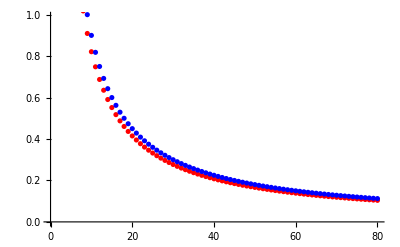

```mathematica
ListPlot[{peakGradientWidth,Table[{n,9/n}, {n,5,80}]},PlotStyle->{Red, Blue} ]
```

```mathematica
subPeakGradientWidth = ParallelTable[{n,NSolve[phiPrime[n,x]== n/12&&x>0,x]}, {n,5,80}];
```

```mathematica
subPeakGradientWidth = subPeakGradientWidth[[2;;]];
```

```mathematica
subPeakGradientWidth[[All, 2]]= x/. subPeakGradientWidth[[All, 2]];
```

```mathematica
Do[subPeakGradientWidth[[i, 2]]= subPeakGradientWidth[[i, 2]][[2]]- subPeakGradientWidth[[i, 2]][[1]],{i, Length[subPeakGradientWidth]}];
```

```mathematica
subPeakGradientWidth
```

{{12,{{x→1.99079}}},{13,{{x→0.0392311},{x→1.95452}}},{14,{{x→0.0741799},{x→1.92152}}},{15,{{x→0.105573},{x→1.89144}}},{16,{{x→0.133975},{x→1.86393}}},{17,{{x→0.159832},{x→1.83869}}},{18,{{x→0.183503},{x→1.81544}}},{19,{{x→0.205281},{x→1.79396}}},{20,{{x→0.225403},{x→1.77405}}},{21,{{x→0.244071},{x→1.75553}}},{22,{{x→0.261451},{x→1.73826}}},{23,{{x→0.277685},{x→1.7221}}},{24,{{x→0.292893},{x→1.70695}}},{25,{{x→0.30718},{x→1.6927}}},{26,{{x→0.320634},{x→1.67928}}},{27,{{x→0.333333},{x→1.6666}}},{28,{{x→0.345346},{x→1.6546}}},{29,{{x→0.356732},{x→1.64323}}},{30,{{x→0.367544},{x→1.63243}}},{31,{{x→0.377829},{x→1.62215}}},{32,{{x→0.387628},{x→1.61236}}},{33,{{x→0.396977},{x→1.60301}}},{34,{{x→0.405911},{x→1.59408}}},{35,{{x→0.41446},{x→1.58553}}},{36,{{x→0.42265},{x→1.57734}}},{37,{{x→0.430505},{x→1.56949}}},{38,{{x→0.438049},{x→1.56195}}},{39,{{x→0.4453},{x→1.5547}}},{40,{{x→0.452277},{x→1.54772}}},{41,{{x→0.458998},{x→1.541}}},{42,{{x→0.465478},{x→1.53452}}},{43,{{x→0.471729},{x→1.52827}}},{44,{{x→0.477767},{x→1.52223}}},{45,{{x→0.483602},{x→1.5164}}},{46,{{x→0.489246},{x→1.51075}}},{47,{{x→0.494709},{x→1.50529}}},{48,{{x→0.5},{x→1.5}}},{49,{{x→0.505128},{x→1.49487}}},{50,{{x→0.510102},{x→1.4899}}},{51,{{x→0.514929},{x→1.48507}}},{52,{{x→0.519616},{x→1.48038}}},{53,{{x→0.524169},{x→1.47583}}},{54,{{x→0.528595},{x→1.4714}}},{55,{{x→0.532901},{x→1.4671}}},{56,{{x→0.53709},{x→1.46291}}},{57,{{x→0.541169},{x→1.45883}}},{58,{{x→0.545141},{x→1.45486}}},{59,{{x→0.549012},{x→1.45099}}},{60,{{x→0.552786},{x→1.44721}}},{61,{{x→0.556467},{x→1.44353}}},{62,{{x→0.560059},{x→1.43994}}},{63,{{x→0.563564},{x→1.43644}}},{64,{{x→0.566987},{x→1.43301}}},{65,{{x→0.570331},{x→1.42967}}},{66,{{x→0.573599},{x→1.4264}}},{67,{{x→0.576793},{x→1.42321}}},{68,{{x→0.579916},{x→1.42008}}},{69,{{x→0.582971},{x→1.41703}}},{70,{{x→0.585961},{x→1.41404}}},{71,{{x→0.588887},{x→1.41111}}},{72,{{x→0.591752},{x→1.40825}}},{73,{{x→0.594558},{x→1.40544}}},{74,{{x→0.597306},{x→1.40269}}},{75,{{x→0.6},{x→1.4}}},{76,{{x→0.60264},{x→1.39736}}},{77,{{x→0.605229},{x→1.39477}}},{78,{{x→0.607768},{x→1.39223}}},{79,{{x→0.610258},{x→1.38974}}},{80,{{x→0.612702},{x→1.3873}}}}

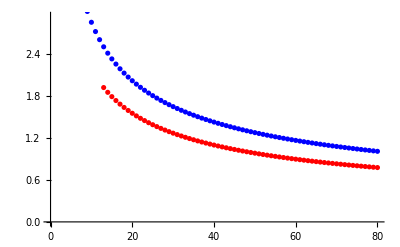

```mathematica
ListPlot[{subPeakGradientWidth,Table[{n,9/n^(1/2)}, {n,5,80}]},PlotStyle->{Red, Blue} ]
```

```mathematica
Table[NIntegrate[phiPrime[n,x]^{1/3},{x,0,Exp[3]}],{n,5,20} ]
```

{{7.20206},{7.44864},{7.63942},{7.79382},{7.92271},{8.03279},{8.12845},{8.21275},{8.28789},{8.35548},{8.41679},{8.47276},{8.52418},{8.57165},{8.61568},{8.65668}}

```mathematica
(*I want to mess around and see if taking the partition to be proportional to √1/f'(x) works well*)
```

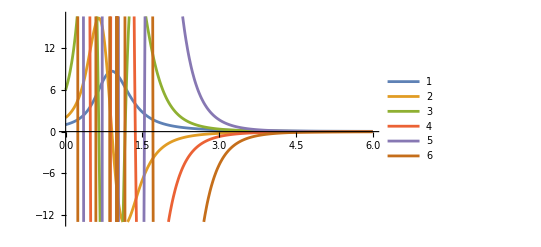

```mathematica
Plot[{Derivative[0,1][ϕ][10,x], Derivative[0,2][ϕ][10,x], Derivative[0,3][ϕ][10,x], Derivative[0,4][ϕ][10,x], Derivative[0,5][ϕ][10,x], Derivative[0,6][ϕ][10,x] },{x,0,6},PlotLegends->{"1","2","3","4", "5","6"}]
```

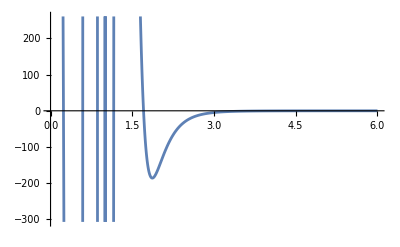

```mathematica
Plot[Derivative[0,6][ϕ][10,x], {x,0,6}]
```

```mathematica
Needs["NumericalCalculus`"]
```

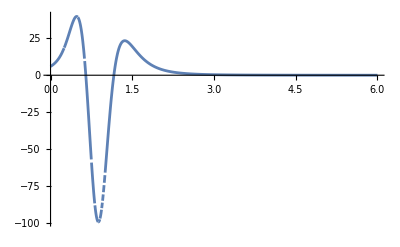

```mathematica
Plot[ND[ϕ[10,x],{x,3},x0], {x0,0,6}, PlotRange->All]
```

```mathematica
ψ[n_, x_, β_,δ_]:= ϕ[n, Exp[-β*Log[1/δ]*x]];
```

```mathematica
Integrate[ψ[n, x, β, δ],{x,-1,1}, Assumptions->δ > 0 && δ<1 && β>0&&n>0]
```

$Aborted

```mathematica
%//FullSimplify
```

-c/β-Log[1-β]+Log[ⅇ^(c/β)-β]+Log[1-β^n]-Log[1-(ⅇ^(-c/β) β)^n]

```mathematica
% /. β->1
```

Infinity::indet: Indeterminate expression -c+-∞+∞+Log[-1+ⅇ^c]-Log[1-(ⅇ^Times[«2»])^n] encountered.

Indeterminate

```mathematica
Integrate[ψ[n, x, 1],{x,0,c}, Assumptions->c>0]
```

c (-1+n)-Log[1-ⅇ^(c n)]+Log[n-ⅇ^c n]

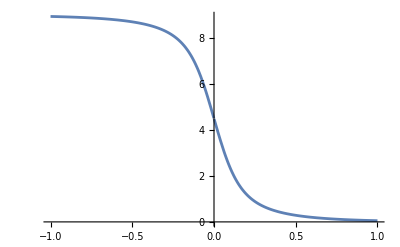

```mathematica
Plot[ψ[10,x,1, Exp[-3]], {x,-1,1}]
```

```mathematica
n=30;
```

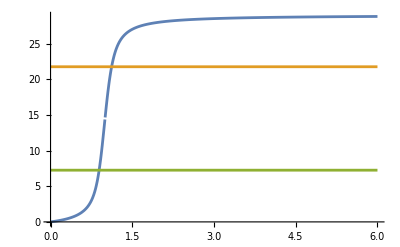

```mathematica
Plot[{ϕ[n,x],3/4*(n-1),1/4*(n-1)}, {x,0,6}]
```

```mathematica
Limit[(ϕ[n,1+h]-(n-1)+ϕ[n,1-h])/h^2,h->0]
```

1/12 (1-n^2)

```mathematica
phiPrimePrime[5,0.99]
```

2.01994

```mathematica
phiPrime[n_,x_]:= Derivative[0,1][ϕ][n,x];
```

```mathematica
phiPrimePrime[n_,x_] := Derivative[0, 2][ϕ][n,x]
```

```mathematica
phiPrimePrimeMax = ParallelTable[FindMaximum[Abs[phiPrimePrime[n,x]],{x,0,1}],{n,10,30}]
```

{{16.2878,{x→0.648997}},{21.0833,{x→0.685448}},{26.7821,{x→0.715399}},{33.463,{x→0.740389}},{41.2052,{x→0.761514}},{50.0877,{x→0.77958}},{60.1898,{x→0.795191}},{63.5297,{x→1.12432}},{75.375,{x→1.1195}},{88.6243,{x→1.11497}},{103.357,{x→1.11072}},{119.653,{x→1.10673}},{137.591,{x→1.10298}},{157.251,{x→1.09947}},{194.436,{x→0.87008}},{219.087,{x→0.875819}},{245.261,{x→0.876076}},{274.509,{x→0.885921}},{305.439,{x→0.890389}},{338.622,{x→0.894525}},{374.135,{x→0.898365}}}

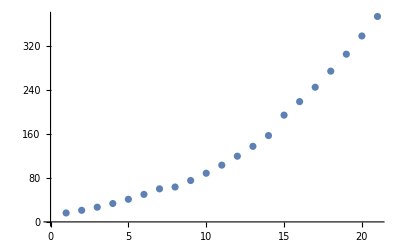

```mathematica
ListPlot[phiPrimePrimeMax[[All, 1]]]
```

```mathematica
phiPrimePrimeMax[[1;3]][[1]]
```

12.3391

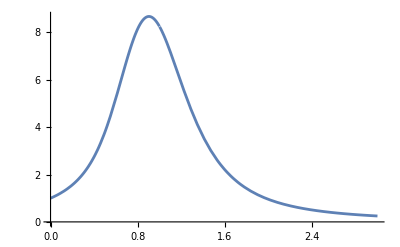

```mathematica
Plot[phiPrime[10,x],{x,0,3}]
```

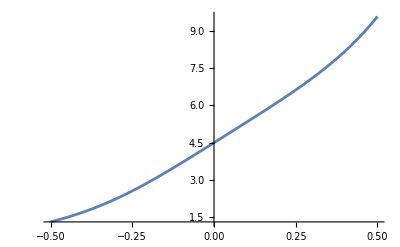

```mathematica
phiApprox[n_,x_]:=- ((n-1)(1+x)^n -n(1+x)^(n-1)+1)/(x(1-x)(1-(1+x)^n));
```

```mathematica
phiApproxLimit[n_,x_]:=-((n-1)Exp[n*x]-n*Exp[n*x]+1)/(x(1-x)(1-Exp[n*x]));
```

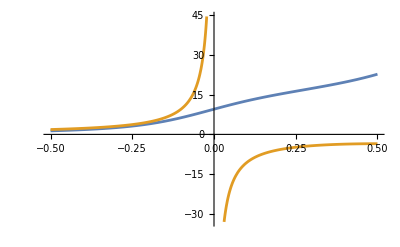

```mathematica
Plot[{phiApprox[20,x], phiApproxLimit[20,x]+1/2},{x,-0.5,0.5}]
```

```mathematica
Limit[phiApproxLimit[n,x],x->0]
```

Indeterminate

```mathematica
Limit[phiApprox[n,x],x->0]
```

1/2 (-1+n)

```mathematica
Apart[f[c, n,-1]]
```

If[ⅇ^c≠1,(ⅇ^c-n (ⅇ^c)^n+(n-1) (ⅇ^c)^(n+1))/((1-ⅇ^c) (1-(ⅇ^c)^n)),(n-1)/2]

```mathematica
Apart[(E^c-n (E^c)^n+(n-1) (E^c)^(n+1))/((1-E^c) (1-(E^c)^n))]//FullSimplify
```

1/(-1+ⅇ^-c)+n+n/(-1+(ⅇ^c)^n)

```mathematica
Apart[(E^c-n (E^c)^n+(n-1) (E^c)^(n+1))/((1-E^c) (1-(E^c)^n))]
```

-1/(-1+ⅇ^c)+(1-(ⅇ^c)^n+(ⅇ^c)^n n)/(-1+(ⅇ^c)^n)

```mathematica
f[c,n,x]
```

If[ⅇ^(-c x)≠1,(ⅇ^(-c x)-n (ⅇ^(-c x))^n+(n-1) (ⅇ^(-c x))^(n+1))/((1-ⅇ^(-c x)) (1-(ⅇ^(-c x))^n)),(n-1)/2]

```mathematica
f[c,n,0]
```

1/2 (-1+n)